# Define functions for MAD data

### Extract the coordinates: X,Y,Z

```mathematica
Clear[GetXYZ];
GetXYZ[x_]:=Module[
{f},
f[y_]:={y[[4]],y[[5]],y[[6]],y[[3]]};
f/@x
]
```

### Extract the coordinates: X,Y

```mathematica
Clear[GetXY];
GetXY[x_]:=Module[
{f},
f[y_]:={y[[4]],y[[5]]};
f/@x
]
```

### Generate: length, height

```mathematica
Clear[CalculateLH];
CalculateLH[x_]:=Module[
{f},
f[y_]:={√((y[[1]]-1880.1405971)^2+(y[[2]]-2090.7822669)^2),y[[3]]-2433.66};
f/@x
]
```

### Calculate distance to a line

```mathematica
Clear[CalculateDistance];
CalculateDistance[x_]:=Module[
{f,a=2.0729557841409147,b=-1.,c=-1806.666058693948},
f[y_]:={Abs[a*y[[1]]+b*y[[2]]+c]/√(a^2+b^2)};
f/@x
]
```

# Get TFS fileBT. Output from 2007: BT_BEAM_COORDINATES.csv BTP_BEAM_COORDINATES.csv

```mathematica
fileBT=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/cmd/BT_28-Jun-2007.csv","CSV"];
fileBTP=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/cmd/BTP_27-Jun-2007.csv","CSV"];
fileBTM=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/cmd/BTM_23-May-2014.csv","CSV"];
fileBTY=Import["http://project-ps-optics.web.cern.ch/project-PS-optics/cps/TransLines/PSB-PS/2014/cmd/BTY_23-May-2014.csv","CSV"];
```

```mathematica
QNO10x=(fileBT[[Range[14,14]]][[1,4]]+fileBT[[Range[15,15]]][[1,4]])/2
QNO10y=(fileBT[[Range[14,14]]][[1,5]]+fileBT[[Range[15,15]]][[1,5]])/2
```

1884.21

2099.21

```mathematica
QNO20x=(fileBT[[Range[16,16]]][[1,4]]+fileBT[[Range[17,17]]][[1,4]])/2
QNO20y=(fileBT[[Range[16,16]]][[1,5]]+fileBT[[Range[17,17]]][[1,5]])/2
```

1885.08

2101.02

```mathematica
QNO30x=(fileBT[[Range[26,26]]][[1,4]]+fileBT[[Range[27,27]]][[1,4]])/2
QNO30y=(fileBT[[Range[26,26]]][[1,5]]+fileBT[[Range[27,27]]][[1,5]])/2
```

1889.82

2110.85

```mathematica
QNO40x=(fileBT[[Range[34,34]]][[1,4]]+fileBT[[Range[35,35]]][[1,4]])/2
QNO40y=(fileBT[[Range[34,34]]][[1,5]]+fileBT[[Range[35,35]]][[1,5]])/2
```

1893.92

2119.34

```mathematica
QNO50x=(fileBT[[Range[38,38]]][[1,4]]+fileBT[[Range[39,39]]][[1,4]])/2
QNO50y=(fileBT[[Range[38,38]]][[1,5]]+fileBT[[Range[39,39]]][[1,5]])/2
```

1894.51

2120.57

```mathematica
Length[fileBT]
```

41

```mathematica
Length[fileBTP]
```

29

```mathematica
Length[fileBTM]
```

23

```mathematica
Length[fileBTY]
```

65

```mathematica
fileBTY[[Range[7,16]]]
```

{{360,IS2,BTYBVT.101.S,1896.25,2133.29,2433.77,1.97883,1.09314,0.1,0,0.2,395.947,-1.57,12-Feb-91,142078},{360,IS2,BTYQDE.104.E,1896.03,2136.61,2434.44,5.37952,,0,0,0.2,395.947,0,12-Feb-91,142079},{360,IS2,BTYQDE.104.S,1896.,2137.1,2434.54,5.87952,0.5,0,0,0.2,395.947,0,12-Feb-91,142080},{360,IS2,BTYQFO.108.E,1895.77,2140.73,2435.28,9.58542,,0,0,0.2,395.947,0,12-Feb-91,142081},{360,IS2,BTYQFO.108.S,1895.74,2141.21,2435.38,10.0854,0.5,0,0,0.2,395.947,0,12-Feb-91,142082},{834,IS2,BTYQDE.113.E,1895.51,2144.84,2436.12,13.7913,,0,0,0.2,395.947,0,12-Feb-91,142083},{834,IS2,BTYQDE.113.S,1895.48,2145.33,2436.22,14.2913,0.5,0,0,0.2,395.947,0,12-Feb-91,142084},{834,IS2,BTYMTV.115.E,1895.31,2148.01,2436.76,17.0298,,0,0,0.2,395.947,0,12-Feb-91,142085},{834,IS2,BTYMTV.115.S,1895.3,2148.2,2436.8,17.2298,0.2,0,0,0.2,395.947,0,12-Feb-91,142086},{834,IS2,BTYBVT.116.E,1895.27,2148.65,2436.89,17.692,,-0.1,0,0.2,395.947,-1.5708,12-Feb-91,142087}}

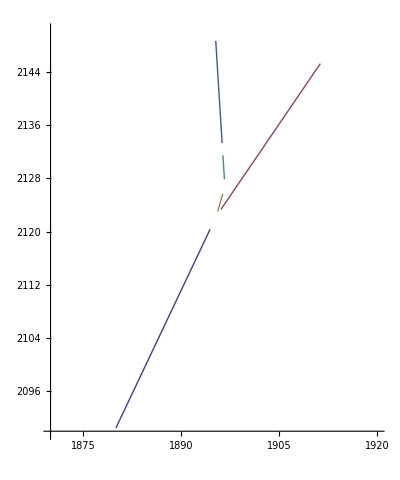

```mathematica
XYBT=GetXY[fileBT[[Range[4,38]]]];
XYBTP=GetXY[fileBTP[[Range[4,29]]]];
XYBTM1=GetXY[fileBTM[[Range[4,10]]]];
XYBTM2=GetXY[fileBTM[[Range[11,23]]]];
XYBTY=GetXY[fileBTY[[Range[7,16]]]];
ListLinePlot[{XYBT,XYBTP,XYBTM1,XYBTM2,XYBTY},PlotRange->{{1870,1920},{2090,2150}},AspectRatio->(2150-2090)/(1920-1870)]
```

# Calculate equations for the straight lines

## BT line

```mathematica
Clear[x];
fileBT[[Range[4,39]]]
XY=GetXY[fileBT[[Range[4,39]]]];
BTline=LinearModelFit[XY,x,x]
```

{{EJ_PT,1,E,1880.,2090.49,2433.66,0.00001,0.,28.6142,0.,0., 14-Jun-1994,},{EJ_PT,1,S,1880.,2090.49,2433.66,0.00002,0.,28.6142,0.,0., 14-Jun-1994,},{BTBVT,10,E,1881.28,2093.14,2433.66,2.94,0.,28.6142,0.,0., 23-Jan-1998,},{BTBVT,10,S,1881.62,2093.86,2433.66,3.74,0.,28.6142,0.,0., 23-Jan-1998,},{BTUES,0,E,1881.72,2094.06,2433.66,3.96763,0.,28.6142,0.,0., 14-Jun-1994,},{BTUES,0,S,1881.94,2094.52,2433.66,4.47913,0.,28.6142,0.,0., 14-Jun-1994,},{BTSMV,10,E,1882.84,2096.37,2433.66,6.53388,0.,28.6142,0.,0., 03-Feb-1999,},{BTSMV,10,S,1883.48,2097.71,2433.66,8.01888,0.,28.6142,0.,0., 03-Feb-1999,},{BTUES,10,E,1883.92,2098.62,2433.66,9.02638,0.,28.6142,0.,0., 14-Jun-1994,},{BTUES,10,S,1884.,2098.78,2433.66,9.21138,0.,28.6142,0.,0., 14-Jun-1994,},{BTQNO,10,E,1884.12,2099.02,2433.66,9.47388,0.,28.6142,0.,0., 27-Jan-1998,},{BTQNO,10,S,1884.3,2099.41,2433.66,9.90388,0.,28.6142,0.,0., 27-Jan-1998,},{BTQNO,20,E,1884.98,2100.82,2433.66,11.4739,0.,28.6142,0.,0., 27-Jan-1998,},{BTQNO,20,S,1885.17,2101.21,2433.66,11.9039,0.,28.6142,0.,0., 27-Jan-1998},{BTKFA,10,E,1886.13,2103.2,2433.66,14.1139,0.,28.6142,0.,0., 14-Jun-1994},{BTKFA,10,S,1887.1,2105.21,2433.66,16.3439,0.,28.6142,0.,0., 14-Jun-1994},{BTBVT,20,E,1887.19,2105.39,2433.66,16.5502,0.,28.6142,0.,0., 10-Feb-1999},{BTBVT,20,S,1887.54,2106.11,2433.66,17.3497,0.,28.6142,0.,0., 10-Feb-1999},{BTUES,20,E,1887.63,2106.3,2433.66,17.5549,0.,28.6142,0.,0., 14-Jun-1994},{BTUES,20,S,1887.71,2106.47,2433.66,17.7399,0.,28.6142,0.,0., 14-Jun-1994},{BTSMV,20,E,1888.92,2108.98,2433.66,20.5289,0.,28.6142,0.,0., 14-Jun-1994},{BTSMV,20,S,1889.57,2110.32,2433.66,22.0189,0.,28.6142,0.,0., 14-Jun-1994},{BTQNO,30,E,1889.73,2110.66,2433.66,22.3939,0.,28.6142,0.,0., 27-Jan-1998},{BTQNO,30,S,1889.92,2111.05,2433.66,22.8239,0.,28.6142,0.,0., 27-Jan-1998},{BTSMV,30,E,1889.97,2111.15,2433.66,22.9419,0.,28.6142,0.,0., 14-Jun-1994},{BTSMV,30,S,1890.34,2111.93,2433.66,23.8059,0.,28.6142,0.,0., 14-Jun-1994},{BTUES,30,E,1891.26,2113.84,2433.66,25.9244,0.,28.6142,0.,0., 14-Jun-1994},{BTUES,30,S,1891.4,2114.12,2433.66,26.2424,0.,28.6142,0.,0., 14-Jun-1994},{BTKFA,20,E,1892.63,2116.66,2433.66,29.0629,0.,28.6142,0.,0., 14-Jun-1994},{BTKFA,20,S,1893.6,2118.67,2433.66,31.2929,0.,28.6142,0.,0., 14-Jun-1994},{BTQNO,40,E,1893.82,2119.15,2433.66,31.8189,0.,28.6142,0.,0., 27-Jan-1998},{BTQNO,40,S,1894.01,2119.53,2433.66,32.2489,0.,28.6142,0.,0., 27-Jan-1998},{BTUES,40,E,1894.1,2119.71,2433.66,32.4489,0.,28.6142,0.,0., 14-Jun-1994},{BTUES,40,S,1894.18,2119.88,2433.66,32.6339,0.,28.6142,0.,0., 14-Jun-1994},{BTQNO,50,E,1894.4,2120.35,2433.66,33.1539,0.,28.6142,0.,0., 14-Jun-1994},{BTQNO,50,S,1894.62,2120.8,2433.66,33.6539,0.,28.6142,0.,0., 14-Jun-1994}}

FittedModel[-1806.67+2.07296 x]

## BTP line

```mathematica
Clear[x];
fileBTP[[Range[4,29]]]
XY=GetXY[fileBTP[[Range[4,29]]]];
BTPline=LinearModelFit[XY,x,x]
```

{{BTPSTP,0,E,1896.07,2123.35,2433.66,1.27186,0,2.04886,},{BTPSTP,0,S,1896.96,2124.63,2433.66,2.82586,0,,},{BTPUES,0,E,1897.56,2125.5,2433.66,3.889,0,3.9815,38.316},{BTPUES,0,S,1897.67,2125.65,2433.66,4.074,0,,},{BTPQNO,10,E,1898.99,2127.56,2433.66,6.4,0,6.6,40.9345},{BTPQNO,10,S,1899.22,2127.89,2433.66,6.8,0,,},{BTPQNO,20,E,1901.28,2130.85,2433.66,10.4,0,10.6,44.9345},{BTPQNO,20,S,1901.5,2131.18,2433.66,10.8,0,,},{BTPUES,10,E,1901.95,2131.83,2433.66,11.5905,0,11.683,46.0175},{BTPUES,10,S,1902.06,2131.98,2433.66,11.7755,0,,},{BTPQNO,30,E,1902.7,2132.9,2433.66,12.9,0,13.1,47.4345},{BTPQNO,30,S,1902.93,2133.23,2433.66,13.3,0,,},{BTPSTP,20,E,1903.77,2134.45,2433.66,14.784,0,15.5125,49.847},{BTPSTP,20,S,1904.6,2135.65,2433.66,16.241,0,,},{BTPQNO,40,E,1905.72,2137.26,2433.66,18.2,0,18.4,52.7345},{BTPQNO,40,S,1905.95,2137.59,2433.66,18.6,0,,},{BTPUES,20,E,1906.34,2138.14,2433.66,19.28,0,19.53,53.8645},{BTPUES,20,S,1906.62,2138.56,2433.66,19.78,0,,},{BTPQNO,50,E,1907.14,2139.3,2433.66,20.69,0,20.89,55.2245},{BTPQNO,50,S,1907.37,2139.63,2433.66,21.09,0,,},{BTPQNO,60,E,1910.39,2143.99,2433.66,26.389,0,26.589,60.9235},{BTPQNO,60,S,1910.62,2144.31,2433.66,26.789,0,,},{BTPUES,30,E,1910.74,2144.49,2433.66,26.999,0,27.0915,61.426},{BTPUES,30,S,1910.84,2144.64,2433.66,27.184,0,,},{BTPMTV,10,E,1911.08,2144.99,2433.66,27.6065,0,27.7645,62.099},{BTPMTV,10,S,1911.26,2145.25,2433.66,27.9225,0,,}}

FittedModel[-609.484+1.44131 x]

## BTM_1 line

```mathematica
Clear[x];
fileBTM[[Range[4,10]]]
XY=GetXY[fileBTM[[Range[4,10]]]];
BTM1line=LinearModelFit[XY,x,x]
```

{{360,BTM,DEPFA.1.E,1895.56,2123.04,2433.66,0.00001,,0,0,0,18.2759,0,14-Dec-95,156377},{360,BTM,DEPFA.1.S,1895.64,2123.29,2433.66,0.25513,0.25512,0,0,0,18.2759,0,14-Dec-95,156378},{360,BTM,BTMMTV.10.E,1895.93,2124.29,2433.66,1.30313,,0,0,0,18.2759,0,14-Dec-95,139040},{360,BTM,BTMMTV.10.S,1895.99,2124.48,2433.66,1.50313,0.2,0,0,0,18.2759,0,14-Dec-95,139041},{360,BTM,BTMQNO.5.E,1896.06,2124.71,2433.66,1.73763,,0,0,0,18.2759,0,14-Dec-95,139038},{360,BTM,BTMQNO.5.S,1896.2,2125.19,2433.66,2.23763,0.5,0,0,0,18.2759,0,14-Dec-95,139039},{360,BTM,BTMBHZ.10.E,1896.35,2125.69,2433.66,2.76108,,0.17537,0,0,18.2759,0,14-Dec-95,139042}}

FittedModel[-4297.57+3.38718 x]

## BTM_2 line

```mathematica
Clear[x];
fileBTM[[Range[11,23]]]
XY=GetXY[fileBTM[[Range[11,23]]]];
BTM2line=LinearModelFit[XY,x,x]
```

{{360,BTM,BTMBHZ.10.S,1896.59,2127.88,2433.66,4.96108,2.2,0.17537,0,0,395.947,0,14-Dec-95,139043},{360,BTM,BTMQNO.10.E,1896.56,2128.32,2433.66,5.40903,,0,0,0,395.947,0,14-Dec-95,139044},{360,BTM,BTMQNO.10.S,1896.53,2128.82,2433.66,5.90903,0.5,0,0,0,395.947,0,14-Dec-95,139045},{360,BTM,BTMDVT.10.E,1896.51,2129.16,2433.66,6.25303,,0,0,0,395.947,0,14-Dec-95,139046},{360,BTM,BTMDVT.10.S,1896.49,2129.45,2433.66,6.53503,0.282,0,0,0,395.947,0,14-Dec-95,139047},{360,BTM,BTMDHZ.10.E,1896.48,2129.63,2433.66,6.71703,,0,0,0,395.947,0,14-Dec-95,139050},{360,BTM,BTMDHZ.10.S,1896.46,2129.91,2433.66,6.99903,0.282,0,0,0,395.947,0,14-Dec-95,139051},{360,BTM,BTMQNO.20.E,1896.44,2130.2,2433.66,7.29203,,0,0,0,395.947,0,14-Dec-95,139048},{360,BTM,BTMQNO.20.S,1896.41,2130.7,2433.66,7.79203,0.5,0,0,0,395.947,0,14-Dec-95,139049},{360,BTM,BTMUES.0.E,1896.4,2130.91,2433.66,7.99753,,0,0,0,395.947,0,14-Dec-95,139054},{360,BTM,BTMUES.0.S,1896.39,2131.09,2433.66,8.18253,0.185,0,0,0,395.947,0,14-Dec-95,139055},{360,BTM,BTMMTV.15.E,1896.37,2131.27,2433.66,8.36653,,0,0,0,395.947,0,14-Dec-95,139052},{360,BTM,BTMMTV.15.S,1896.36,2131.47,2433.66,8.56653,0.2,0,0,0,395.947,0,14-Dec-95,139053}}

FittedModel[31880.-15.6871 x]

## BTY line

```mathematica
Clear[x];
fileBTY[[Range[7,16]]]
XY=GetXY[fileBTM[[Range[7,16]]]];
BTYline=LinearModelFit[XY,x,x]
```

{{360,IS2,BTYBVT.101.S,1896.25,2133.29,2433.77,1.97883,1.09314,0.1,0,0.2,395.947,-1.57,12-Feb-91,142078},{360,IS2,BTYQDE.104.E,1896.03,2136.61,2434.44,5.37952,,0,0,0.2,395.947,0,12-Feb-91,142079},{360,IS2,BTYQDE.104.S,1896.,2137.1,2434.54,5.87952,0.5,0,0,0.2,395.947,0,12-Feb-91,142080},{360,IS2,BTYQFO.108.E,1895.77,2140.73,2435.28,9.58542,,0,0,0.2,395.947,0,12-Feb-91,142081},{360,IS2,BTYQFO.108.S,1895.74,2141.21,2435.38,10.0854,0.5,0,0,0.2,395.947,0,12-Feb-91,142082},{834,IS2,BTYQDE.113.E,1895.51,2144.84,2436.12,13.7913,,0,0,0.2,395.947,0,12-Feb-91,142083},{834,IS2,BTYQDE.113.S,1895.48,2145.33,2436.22,14.2913,0.5,0,0,0.2,395.947,0,12-Feb-91,142084},{834,IS2,BTYMTV.115.E,1895.31,2148.01,2436.76,17.0298,,0,0,0.2,395.947,0,12-Feb-91,142085},{834,IS2,BTYMTV.115.S,1895.3,2148.2,2436.8,17.2298,0.2,0,0,0.2,395.947,0,12-Feb-91,142086},{834,IS2,BTYBVT.116.E,1895.27,2148.65,2436.89,17.692,,-0.1,0,0.2,395.947,-1.5708,12-Feb-91,142087}}

FittedModel[-13841.3+8.42059 x]

# Calculate starting angle for the BT line and angle between BT and BTP

```mathematica
a1=BTline[[1,2,2]]
```

2.07296

```mathematica
Clear[angle];
angle = angle/.Solve[ Sin[angle]==a1/√(1+a1^2),angle][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.12133

```mathematica
angle+2*π  (* Angle used for GEODE *)
```

7.40451

tan(Ɵ)=-Graphics-

```mathematica
a1=BTline[[1,2,2]];
a2=BTPline[[1,2,2]];
Clear[BTBTPangle];
BTBTPangle=BTBTPangle/.Solve[Tan[BTBTPangle]==Abs[(a2-a1)/(1+a1*a2)],BTBTPangle][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.15709

# Calculate angle between BT and BTM1

tan(Ɵ)=-Graphics-

```mathematica
a1=BTline[[1,2,2]];
a2=BTM1line[[1,2,2]];
Clear[BTBTM1angle];
BTBTM1angle=BTBTM1angle/.Solve[Tan[BTBTM1angle]==Abs[(a2-a1)/(1+a1*a2)],BTBTM1angle][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.162395

```mathematica
0.16239528906822892
```

```mathematica
0.16239528906822892
```

# Calculate angle between BTM1 and BTM2

tan(Ɵ)=-Graphics-

```mathematica
a1=BTM1line[[1,2,2]];
a2=BTM2line[[1,2,2]];
Clear[BTM1BTM2angle];
BTM1BTM2angle=BTM1BTM2angle/.Solve[Tan[BTM1BTM2angle]==Abs[(a2-a1)/(1+a1*a2)],BTM1BTM2angle][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.350736

```mathematica
0.350736179829213
```

```mathematica
0.350736179829213
```

# Calculate angle between BTM2 and BTY

tan(Ɵ)=-Graphics-

```mathematica
a1=BTM2line[[1,2,2]];
a2=BTYline[[1,2,2]];
Clear[BTM2BTYangle];
BTM2BTYangle= BTM2BTYangle/.Solve[Tan[BTM2BTYangle]==Abs[(a2-a1)/(1+a1*a2)],BTM2BTYangle][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.181863

```mathematica
0.18186327664189633
```

# Deflection point for BT - BTP

```mathematica
Clear[x];

a1=BTline[[1,2,2]];
b1=BTline[[1,2,1]];
a2=BTPline[[1,2,2]];
b2=BTPline[[1,2,1]];
crossBTBTP={x,y}/.Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}][[1]]
```

{1895.35,2122.3}

```mathematica
{1895.3466844371555,2122.303813762359}
```

{1895.35,2122.3}

Length before BHZ10

```mathematica
StartBT=GetXYZ[fileBT[[Range[4,4]]]][[1]][[Range[1,2]]]
LengthBeforeBHZ10 = √((crossBTBTP[[1]]-StartBT[[1]])^2+(crossBTBTP[[2]]-StartBT[[2]])^2)
```

{1880.,2090.49}

35.3239

```mathematica
StartBTNEW={1880.1405971,2090.7822669}
```

{1880.14,2090.78}

Difference in starting point :

```mathematica
DiffLength=√((StartBTNEW[[1]]-StartBT[[1]])^2+(StartBTNEW[[2]]-StartBT[[2]])^2)
```

0.326284

```mathematica
LengthBTLineToDeflecNEW=LengthBeforeBHZ10 -DiffLength
```

34.9976

```mathematica
LengthBeforeBHZ10NEW=34.228700
```

34.2287

```mathematica
LDeflectBHZ10=1.5334*2*Tan[0.157089/2]/0.157089
```

1.53656

```mathematica
LengthBeforeBHZ10NEW+LDeflectBHZ10/2
```

34.997

```mathematica
LengthBTLineToDeflecNEW-34.99698055215014
```

0.000633777

```mathematica
(LengthBTLineToDeflecNEW-LengthBeforeBHZ10NEW)*2
```

1.53783

```mathematica
1.5327/Cos[0.157089/2]
```

1.53744

```mathematica
1.53428*2*Tan[0.157089/2]/0.157089
```

1.53744

# Deflection point for BT - BTM1

```mathematica
Clear[x];

a1=BTline[[1,2,2]];
b1=BTline[[1,2,1]];
a2=BTM1line[[1,2,2]];
b2=BTM1line[[1,2,1]];
crossBTBTM1={x,y}/.Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}][[1]]
```

{1895.35,2122.3}

```mathematica
{1895.3466851419835,2122.303815223436}
```

{1895.35,2122.3}

# Deflection point for BTM1 - BTM2

```mathematica
Clear[x];

a1=BTM1line[[1,2,2]];
b1=BTM1line[[1,2,1]];
a2=BTM2line[[1,2,2]];
b2=BTM2line[[1,2,1]];
crossBTM1BTM2={x,y}/.Solve[y==a1*x+b1&&y==a2*x+b2,{x,y}][[1]]
```

{1896.66,2126.76}

```mathematica
{1896.6624987552193,2126.7607103746086}
```

{1896.66,2126.76}

# End of BT line

```mathematica
Clear[x];
GetXYZ[fileBT[[Range[214,214]]]]
XY=GetXY[fileBT[[Range[214,214]]]];
```

Part::partw: Part {214} of {{"Listing des Points Faisceau de BT", "", "", "", "", "", "", "", "", "Jour de l'impression:", "", " 28-JUN-2007", ""}, {"", "", "", "", "", "", "", "", "", "", "", "", ""}, {"Classe", "Num\[EAcute]ro", "Pt", "X", "Y", "Z", "Dist.cumul\[EAcute]e", "Tilt", "Gisement", "D\[EAcute]flexion", "Pente", "Jour", "Commentaire"}, « 35 », {"BTQNO", 50, "S", 1894.62, 2120.8, 2433.66, 33.6539, 0., 28.6142, 0., 0., " 14-Jun-1994"}, {"BTBHZ", 10, "E", 1895.01, 2121.61, 2433.66, 34.555, 0., 28.6142, 0.081195, 0., " 14-Jun-1994"}, {"BTBHZ", 10, "S", 1895.56, 2123.04, 2433.66, 36.0877, 0., 18.2759, 0.081195, 0., " 14-Jun-1994"}} does not exist.

Part::partw: Part 4 of {214} does not exist.

Part::partw: Part 5 of {214} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{214} ⟦ 4 ⟧, {214} ⟦ 5 ⟧, {214} ⟦ 6 ⟧, {214} ⟦ 3 ⟧} is neither an integer nor a list of integers.

{{EJ_PT,1,E,1880.,2090.49,2433.66,0.00001,0.,28.6142,0.,0., 14-Jun-1994,},{EJ_PT,1,S,1880.,2090.49,2433.66,0.00002,0.,28.6142,0.,0., 14-Jun-1994,},{BTBVT,10,E,1881.28,2093.14,2433.66,2.94,0.,28.6142,0.,0., 23-Jan-1998,},{Classe,Numéro,Pt,X,Y,Z,Dist.cumulée,Tilt,Gisement,Déflexion,Pente,Jour,Commentaire}}⟦{{214}⟦4⟧,{214}⟦5⟧,{214}⟦6⟧,{214}⟦3⟧}⟧

Part::partw: Part {214} of {{"Listing des Points Faisceau de BT", "", "", "", "", "", "", "", "", "Jour de l'impression:", "", " 28-JUN-2007", ""}, {"", "", "", "", "", "", "", "", "", "", "", "", ""}, {"Classe", "Num\[EAcute]ro", "Pt", "X", "Y", "Z", "Dist.cumul\[EAcute]e", "Tilt", "Gisement", "D\[EAcute]flexion", "Pente", "Jour", "Commentaire"}, « 35 », {"BTQNO", 50, "S", 1894.62, 2120.8, 2433.66, 33.6539, 0., 28.6142, 0., 0., " 14-Jun-1994"}, {"BTBHZ", 10, "E", 1895.01, 2121.61, 2433.66, 34.555, 0., 28.6142, 0.081195, 0., " 14-Jun-1994"}, {"BTBHZ", 10, "S", 1895.56, 2123.04, 2433.66, 36.0877, 0., 18.2759, 0.081195, 0., " 14-Jun-1994"}} does not exist.

Part::partw: Part 4 of {214} does not exist.

Part::partw: Part 5 of {214} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification {{214} ⟦ 4 ⟧, {214} ⟦ 5 ⟧} is neither an integer nor a list of integers.

```mathematica
crossENDBI={XY[[1,1]],XY[[1,2]]}
```

{{EJ_PT,1,E,1880.,2090.49,2433.66,0.00001,0.,28.6142,0.,0., 14-Jun-1994,},{EJ_PT,1,S,1880.,2090.49,2433.66,0.00002,0.,28.6142,0.,0., 14-Jun-1994,}}

```mathematica
(* crossENDBI={1880.067574,2109.655523} *) (* From NEW survey fileBT *)
```

Length from deflection point of BHZ40 to end of BI line

```mathematica
LengthBeforeBHZ20 = √((crossBHZ40[[1]]-crossENDBI[[1]])^2+(crossBHZ40[[2]]-crossENDBI[[2]])^2)
```

Part::partd: Part specification crossBHZ40 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification crossBHZ40 ⟦ 2 ⟧ is longer than depth of object.

{√((-EJ_PT+crossBHZ40⟦1⟧)^2+(-EJ_PT+crossBHZ40⟦2⟧)^2),√((-1+crossBHZ40⟦1⟧)^2+(-1+crossBHZ40⟦2⟧)^2),√((-E+crossBHZ40⟦1⟧)^2+(-S+crossBHZ40⟦2⟧)^2),√((-1880.+crossBHZ40⟦1⟧)^2+(-1880.+crossBHZ40⟦2⟧)^2),√((-2090.49+crossBHZ40⟦1⟧)^2+(-2090.49+crossBHZ40⟦2⟧)^2),√((-2433.66+crossBHZ40⟦1⟧)^2+(-2433.66+crossBHZ40⟦2⟧)^2),√((-0.00001+crossBHZ40⟦1⟧)^2+(-0.00002+crossBHZ40⟦2⟧)^2),√((0.+crossBHZ40⟦1⟧)^2+(0.+crossBHZ40⟦2⟧)^2),√((-28.6142+crossBHZ40⟦1⟧)^2+(-28.6142+crossBHZ40⟦2⟧)^2),√((0.+crossBHZ40⟦1⟧)^2+(0.+crossBHZ40⟦2⟧)^2),√((0.+crossBHZ40⟦1⟧)^2+(0.+crossBHZ40⟦2⟧)^2),√((- 14-Jun-1994+crossBHZ40⟦1⟧)^2+(- 14-Jun-1994+crossBHZ40⟦2⟧)^2),√((-+crossBHZ40⟦1⟧)^2+(-+crossBHZ40⟦2⟧)^2)}

# Distance from START-BT to center of KFA10

```mathematica
XYZ[[Range[15,16]]]
KFA10=CalculateLH[XYZ[[Range[15,16]]]];
XYZ[[Range[15,15]]]
XYZ[[Range[16,16]]]
(XYZ[[Range[15,15]]]+XYZ[[Range[16,16]]])/2
```

Part::partd: Part specification XYZ ⟦ {15, 16} ⟧ is longer than depth of object.

XYZ⟦{15,16}⟧

Part::partd: Part specification XYZ ⟦ {15, 16} ⟧ is longer than depth of object.

Part::partd: Part specification XYZ ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification XYZ ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Part::partw: Part 3 of {15, 16} does not exist.

Part::pspec: Part specification {2789.89, -2433.66 + {15, 16} ⟦ 3 ⟧} is neither an integer nor a list of integers.

Part::partd: Part specification XYZ ⟦ {15} ⟧ is longer than depth of object.

XYZ⟦{15}⟧

Part::partd: Part specification XYZ ⟦ {16} ⟧ is longer than depth of object.

XYZ⟦{16}⟧

Part::partd: Part specification XYZ ⟦ {15} ⟧ is longer than depth of object.

Part::partd: Part specification XYZ ⟦ {16} ⟧ is longer than depth of object.

Part::partd: Part specification XYZ ⟦ {15} ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

1/2 (XYZ⟦{15}⟧+XYZ⟦{16}⟧)

```mathematica
KFA10[[1,1]]
KFA10[[2,1]]
(KFA10[[1,1]]+KFA10[[2,1]])/2
```

√((-1880.14+XYZ⟦1⟧)^2+(-2090.78+XYZ⟦2⟧)^2)

2789.89

1/2 (2789.89+√((-1880.14+XYZ⟦1⟧)^2+(-2090.78+XYZ⟦2⟧)^2))

```mathematica
13.787598257669705+0.925
```

14.7126

```mathematica
xolav=1893.02868150
yolav=2117.49868735
√((xolav-1880.140597)^2+(yolav-2090.782267)^2)
```

1893.03

2117.5

29.6626

# Distance from START-BT to END-BT

```mathematica
BTSTART={1880.140597106634686,2090.782266902764604}
BTEND={1895.012875308090315,2121.611842023826284}
```

{1880.14059710663469,2090.7822669027646}

{1895.01287530809032,2121.61184202382628}

```mathematica
√((BTEND[[1]]-BTSTART[[1]])^2+(BTEND[[2]]-BTSTART[[2]])^2)
```

34.22933480286577